# Rigid bodies, plastic impact

```mathematica
param={l1->7.11,l2->7.11,m1->1336/2,m2->1336/2,mb->10000,mO->1000,r->0.285,γ->0.5};
paramExtraction={l1->7.11,l2->7.11,m1->1336/2,m2->1336/2,mb->10000,r->0.285,γ->0.5};
```

```mathematica
θ00=π/2;q10=0;q20=π/2;xb0=4;yb0=2;
```

```mathematica
paramScheme={θ0[t]->θ00,q1[t]->q10,q2[t]->q20,xb[t]->xb0,yb[t]->yb0};
```

## Kinematics

## Manipulator

We start with a simple manipulator, moving base (that mimics the spacecraft position and orientation) and two rotational links.

```mathematica
Mrotztrasl[α_,point_]:={{Cos[α],-Sin[α],0,point[[1]]},{Sin[α],Cos[α],0,point[[2]]},{0,0,1,point[[3]]},{0,0,0,1}};
Mrotztrasl[α,{p1,p2,p3}]//MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

```mathematica
Mfb=Mrotztrasl[0,{xb[t],yb[t],0}];
```

```mathematica
Mb0=Mrotztrasl[θ0[t],{0,0,0}];
```

```mathematica
Mf0=Mfb.Mb0;Mf0//MatrixForm
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | xb[t]
Sin[θ0[t]] | Cos[θ0[t]] | 0 | yb[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M01=Mrotztrasl[q1[t],{l1 Cos[q1[t]],l1 Sin[q1[t]],0}];M01//MatrixForm
```

(Cos[q1[t]] | -Sin[q1[t]] | 0 | l1 Cos[q1[t]]
Sin[q1[t]] | Cos[q1[t]] | 0 | l1 Sin[q1[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M12=Mrotztrasl[q2[t],{l2 Cos[q2[t]],l2 Sin[q2[t]],0}];M12//MatrixForm
```

(Cos[q2[t]] | -Sin[q2[t]] | 0 | l2 Cos[q2[t]]
Sin[q2[t]] | Cos[q2[t]] | 0 | l2 Sin[q2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02=Simplify[M01.M12];
```

```mathematica
Mf1=Simplify[Mf0.M01];
```

```mathematica
Mf2=Simplify[Mf1.M12];
```

### Origin points

```mathematica
origin={0,0,0,1};
```

```mathematica
Ob=Mfb.origin;Ob//MatrixForm
```

(xb[t]
yb[t]
0
1)

```mathematica
O1=Mf1.origin;O1//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+yb[t]
0
1)

```mathematica
EE=Simplify[Mf2.origin];EE//MatrixForm
```

(l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]]+xb[t]
l1 Sin[q1[t]+θ0[t]]+l2 Sin[q1[t]+q2[t]+θ0[t]]+yb[t]
0
1)

Jacobian matrixOb:

```mathematica
J=FullSimplify[D[EE[[1;;2]],{{xb[t],yb[t],θ0[t],q1[t],q2[t]}}]];J//MatrixForm
```

(1 | 0 | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]] | -l2 Sin[q1[t]+q2[t]+θ0[t]]
0 | 1 | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l1 Cos[q1[t]+θ0[t]]+l2 Cos[q1[t]+q2[t]+θ0[t]] | l2 Cos[q1[t]+q2[t]+θ0[t]])

```mathematica
J. D[{xb[t],yb[t],θ0[t],q1[t],q2[t]},t]==D[EE[[1;;2]],t]//Simplify
```

True

### Plot a 2D scheme of the robot

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
labels={"xf","yf"};
```

```mathematica
For[i=1,i<3,i++,u={0,0};(*initializing u as a null 3 elements vector*)u⟦i⟧=1;(*Setting the i-th element of u equal to 1,to have a unit vector*)RF0arrow[i]=Graphics[{Thickness[0.010],Red,Arrowheads[0.04],
Text[labels⟦i⟧,2 u+0.07],Arrow[{{0,0},2 u}]},Axes->True]];
```

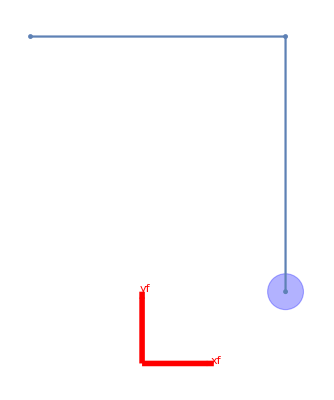

```mathematica
Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],RobotPlot,RF0arrow[1],RF0arrow[2]}]
```

```mathematica
paraml={l1->2.0,l2->3.0};
```

```mathematica
Manipulate[Show[{ListLinePlot[{Ob[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},O1[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},EE[[1;;2]]/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5}}/.paraml,PlotRange->{{-5,8},{-5,8}},AspectRatio->1,PlotMarkers->{Automatic, 5}]},Block[{r=0.5},Graphics[{EdgeForm[Thick],Blue,Opacity[0.3],Disk[Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},r],Thickness[0.007],Opacity[0.5],Red,Arrowheads[0.04],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 /.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1/.paraml/.paramScheme}}],Blue,Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]-l1 Sin[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Cos[a3]/.paraml/.paramScheme}}],Arrow[{Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5},{(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[1]]+l1 Cos[a3]/.paraml/.paramScheme,(Ob[[1;;2]]/.param/.{xb[t]->a1,yb[t]->a2,θ0[t]->a3,q1[t]->a4,q2[t]->a5})[[2]]+l1 Sin[a3]/.paraml/.paramScheme}}]}]],RF0arrow[1],RF0arrow[2]],{a1,0,3},{a2,0,3},{a3,0,π/4},{a4,0,π/4},{a5,0,π/4}]
```

## Object

-Graphics-

Let’s consider a circula spinning satellite. In 2D, we have 3 DoF: xb, yOb, and rotation around z.
Coordinats refered to the COM:

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

The jacobian describe the relationship between the velocityOb of the dof and the contact point:

```mathematica
MfO0=Mrotztrasl[0,{xO[t],yO[t],0}];MfO0//MatrixForm
```

(1 | 0 | 0 | xO[t]
0 | 1 | 0 | yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO0O1=Mrotztrasl[Ω[t],{0,0,0}];MO0O1//MatrixForm
```

(Cos[Ω[t]] | -Sin[Ω[t]] | 0 | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MO1O2=Mrotztrasl[γ,{r Cos[γ] ,r Sin[γ],0}];MO1O2//MatrixForm
```

(Cos[γ] | -Sin[γ] | 0 | r Cos[γ]
Sin[γ] | Cos[γ] | 0 | r Sin[γ]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
MfO1=MfO0.MO0O1;
MfO2=Simplify[MfO0.MO0O1.MO1O2];MfO2//MatrixForm
```

(Cos[γ+Ω[t]] | -Sin[γ+Ω[t]] | 0 | r Cos[γ+Ω[t]]+xO[t]
Sin[γ+Ω[t]] | Cos[γ+Ω[t]] | 0 | r Sin[γ+Ω[t]]+yO[t]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
contactP=(MfO2.{0,0,0,1})[[1;;2]];contactP//MatrixForm
velContactP=D[contactP,t];velContactP//MatrixForm
```

(r Cos[γ+Ω[t]]+xO[t]
r Sin[γ+Ω[t]]+yO[t])

(xO'[t]-r Sin[γ+Ω[t]] Ω'[t]
yO'[t]+r Cos[γ+Ω[t]] Ω'[t])

```mathematica
Jo=D[contactP,{{xO[t],yO[t],Ω[t]}}];Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

```mathematica
Transpose[Jo]//MatrixForm
```

(1 | 0
0 | 1
-r Sin[γ+Ω[t]] | r Cos[γ+Ω[t]])

```mathematica
Jo.ψ'==velContactP//Simplify
```

True

## Dynamics

## Manipulator

### IR method

The mass is considered distributed, hence the pseudo inertia tensor can be written like this:

```mathematica
Ixb=1/4 mb r^2;
Iyb=1/4 mb r^2;
Izb=0;
Ix1=1/3m1 l1^2;
Ix2=1/3 m2 l2^2;
```

Inertia frame in the com of the round base:

```mathematica
J00={{Ixb,0,0,0},{0,Iyb,0,0},{0,0,Izb,0},{0,0,0,mb}};J00//MatrixForm
```

((mb r^2)/4 | 0 | 0 | 0
0 | (mb r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mb)

```mathematica
J0f=Simplify[Mf0.J00.Transpose[Mf0]];J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
J11={{Ix1,0,0,-l1/2 m1},{0,0,0,0},{0,0,0,0},{-l1/2 m1,0,0,m1}};J11//MatrixForm
```

((l1^2 m1)/3 | 0 | 0 | -(l1 m1)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l1 m1)/2 | 0 | 0 | m1)

```mathematica
J1f=Simplify[Mf1.J11.Transpose[Mf1]];
```

```mathematica
J22={{Ix2,0,0,-l2/2 m2},{0,0,0,0},{0,0,0,0},{-l2/2 m2,0,0,m2}};J22//MatrixForm
```

((l2^2 m2)/3 | 0 | 0 | -(l2 m2)/2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(l2 m2)/2 | 0 | 0 | m2)

```mathematica
J2f=Simplify[Mf2.J22.Transpose[Mf2]];
```

```mathematica
Wf0=Simplify[D[Mf0,t].Inverse[Mf0]];Wf0//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb=Simplify[D[Mfb,t].Inverse[Mfb]];Wfb//MatrixForm
```

(0 | 0 | 0 | xb'[t]
0 | 0 | 0 | yb'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0=Simplify[D[Mb0,t].Inverse[Mb0]];Wb0//MatrixForm
```

(0 | -θ0'[t] | 0 | 0
θ0'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wb0Ff=Simplify[Mfb.Wb0.Inverse[Mfb]];Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | yb[t] θ0'[t]
θ0'[t] | 0 | 0 | -xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wfb+Wb0Ff//MatrixForm
```

(0 | -θ0'[t] | 0 | xb'[t]+yb[t] θ0'[t]
θ0'[t] | 0 | 0 | yb'[t]-xb[t] θ0'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Lfbx=({{0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}});
Lfby=({{0, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 0, 0}, {0, 0, 0, 0}});
```

```mathematica
Lb0=Wb0/θ0'[t];
```

```mathematica
Lb0Ff=Simplify[Mf0.Lb0.Inverse[Mf0]];Lb0Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W01=Simplify[D[M01,t].Inverse[M01]];W01//MatrixForm
```

(0 | -q1'[t] | 0 | 0
q1'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L01=W01/q1'[t];
```

```mathematica
L01Ff=Simplify[Mf0.L01.Inverse[Mf0]];L01Ff//MatrixForm
```

(0 | -1 | 0 | yb[t]
1 | 0 | 0 | -xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf1=Simplify[D[Mf1,t].Inverse[Mf1]];Wf1//MatrixForm
```

(0 | -q1'[t]-θ0'[t] | 0 | xb'[t]+yb[t] (q1'[t]+θ0'[t])
q1'[t]+θ0'[t] | 0 | 0 | yb'[t]-xb[t] (q1'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
W12=Simplify[D[M12,t].Inverse[M12]];W12//MatrixForm
```

(0 | -q2'[t] | 0 | 0
q2'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
L12=W12/q2'[t];
L12Ff=Simplify[Mf1.L12.Inverse[Mf1]];L12Ff//MatrixForm
```

(0 | -1 | 0 | l1 Sin[q1[t]+θ0[t]]+yb[t]
1 | 0 | 0 | -l1 Cos[q1[t]+θ0[t]]-xb[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Wf2=Simplify[D[Mf2,t].Inverse[Mf2]];Wf2//MatrixForm
```

(0 | -q1'[t]-q2'[t]-θ0'[t] | 0 | l1 Sin[q1[t]+θ0[t]] q2'[t]+xb'[t]+yb[t] (q1'[t]+q2'[t]+θ0'[t])
q1'[t]+q2'[t]+θ0'[t] | 0 | 0 | -l1 Cos[q1[t]+θ0[t]] q2'[t]+yb'[t]-xb[t] (q1'[t]+q2'[t]+θ0'[t])
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
T1=Simplify[1/2Tr[Wf0.J0f.Transpose[Wf0]]];
T2=Simplify[1/2Tr[Wf1.J1f.Transpose[Wf1]]];
T3=Simplify[1/2Tr[Wf2.J2f.Transpose[Wf2]]];
```

The potential energy of body i, denoted by Ui, consists of two parts; one due to the gravity gradient and the other due to the elastic strain energy stored in the flexbible body. The effect of the former is much smaller than the latter and is neglected here. Hence the potential energy of a rigid body is equal to zero.

```mathematica
L=T1+T2+T3;
```

ByOb neglecting the constraints forces (since theyOb don’t affect the lagrange equation), we get the actions matrices:

```mathematica
actionMatrix[cx_,cy_,cz_,fx_,fy_,fz_]:={{0,-cz,cy,fx},{cz,0,-cx,fy},{-cy,cx,0,fz},{-fx,-fy,-fz,0}};
```

```mathematica
ϕ0b=actionMatrix[0,0,τ1-τ2,Fx,Fy,0];ϕ0b//MatrixForm
```

(0 | -τ1+τ2 | 0 | Fx
τ1-τ2 | 0 | 0 | Fy
0 | 0 | 0 | 0
-Fx | -Fy | 0 | 0)

```mathematica
ϕbf=FullSimplify[Mf0.ϕ0b.Transpose[Mf0]];
```

```mathematica
ϕ11=actionMatrix[0,0,τ2-τ3,0,0,0];ϕ11//MatrixForm
ϕ1f=FullSimplify[Mf1.ϕ11.Transpose[Mf1]];ϕ1f//MatrixForm
```

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | -τ2+τ3 | 0 | 0
τ2-τ3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
ϕ22=actionMatrix[0,0,τ3,0,0,0];
ϕ2f=FullSimplify[Mf2.ϕ22.Transpose[Mf2]];
```

Let’s derivate the non-lagrangian components:

```mathematica
PSS[Mat1_,Mat2_]:=Mat1[[3,2]]*Mat2[[3,2]]+Mat1[[1,3]]*Mat2[[1,3]]+Mat1[[2,1]]*Mat2[[2,1]]+Mat1[[1,4]]*Mat2[[1,4]]+Mat1[[2,4]]*Mat2[[2,4]]+Mat1[[3,4]]*Mat2[[3,4]];
```

```mathematica
f1=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfbx]]
f2=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lfby]]
f3=FullSimplify[PSS[(ϕbf+ϕ1f+ϕ2f),Lb0Ff]]
f4=FullSimplify[PSS[(ϕ1f+ϕ2f),L01Ff]]
f5=Simplify[PSS[(ϕ2f),L12Ff]]
```

Fx Cos[θ0[t]]-Fy Sin[θ0[t]]

Fy Cos[θ0[t]]+Fx Sin[θ0[t]]

τ1

τ2

τ3

```mathematica
eq1=Simplify[D[D[L,xb'[t]],t]-D[L,xb[t]]-f1];
eq2=Simplify[D[D[L,yb'[t]],t]-D[L,yb[t]]-f2];
eq3=Simplify[D[D[L,θ0'[t]],t]-D[L,θ0[t]]-f3];
eq4=Simplify[D[D[L,q1'[t]],t]-D[L,q1[t]]-f4];
eq5=Simplify[D[D[L,q2'[t]],t]-D[L,q2[t]]-f5];
```

```mathematica
{c,A}=FullSimplify[Normal@CoefficientArrays[{eq1,eq2,eq3,eq4,eq5},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M=A[[1;;5,1;;5]];
u=-A[[1;;5,6;;10]];
```

```mathematica
MatrixForm[M]
```

(m1+m2+mb | 0 | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | -1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]]
0 | m1+m2+mb | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]]
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/6 (2 l2^2 m2+2 l1^2 (m1+3 m2)+3 mb r^2+6 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]]-l2 m2 Sin[q1[t]+q2[t]+θ0[t]]) | 1/2 (l1 (m1+2 m2) Cos[q1[t]+θ0[t]]+l2 m2 Cos[q1[t]+q2[t]+θ0[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/3 (l2^2 m2+l1^2 (m1+3 m2)+3 l1 l2 m2 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]])
-1/2 l2 m2 Sin[q1[t]+q2[t]+θ0[t]] | 1/2 l2 m2 Cos[q1[t]+q2[t]+θ0[t]] | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | 1/6 l2 m2 (2 l2+3 l1 Cos[q2[t]]) | (l2^2 m2)/3)

```mathematica
MatrixForm[u]
```

(Cos[θ0[t]] | -Sin[θ0[t]] | 0 | 0 | 0
Sin[θ0[t]] | Cos[θ0[t]] | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)

```mathematica
MatrixForm[c]
```

(1/2 (-l1 (m1+2 m2) Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Cos[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2+l2 m2 Sin[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
1/2 (-l1 (m1+2 m2) Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])^2-l2 m2 Cos[q1[t]+θ0[t]] Sin[q2[t]] (q1'[t]+q2'[t]+θ0'[t])^2-l2 m2 Cos[q2[t]] Sin[q1[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])^2)
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
-1/2 l1 l2 m2 Sin[q2[t]] q2'[t] (2 q1'[t]+q2'[t]+2 θ0'[t])
1/2 l1 l2 m2 Sin[q2[t]] (q1'[t]+θ0'[t])^2)

Equation of motion: Mp^(..)+ c = u

### Classic Lagrangian method

```mathematica
Ob2D=(Mfb.{0,0,0,1})[[1;;2]];
O12D=(Mf1.{-l1/2,0,0,1})[[1;;2]]
EE2D=(Mf2.{-l2/2,0,0,1})[[1;;2]];
```

{1/2 l1 Cos[q1[t]+θ0[t]]+xb[t],1/2 l1 Sin[q1[t]+θ0[t]]+yb[t]}

```mathematica
vb=D[Ob2D,t]
v1=D[O12D,t]
v2=D[EE2D,t]
```

{xb'[t],yb'[t]}

{xb'[t]-1/2 l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t]),yb'[t]+1/2 l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])}

{xb'[t]-l1 Sin[q1[t]+θ0[t]] (q1'[t]+θ0'[t])-1/2 l2 Sin[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t]),yb'[t]+l1 Cos[q1[t]+θ0[t]] (q1'[t]+θ0'[t])+1/2 l2 Cos[q1[t]+q2[t]+θ0[t]] (q1'[t]+q2'[t]+θ0'[t])}

```mathematica
vbsquare=Simplify[vb[[1]]^2+vb[[2]]^2];
v1square=Simplify[v1[[1]]^2+v1[[2]]^2];
v2square=Simplify[v2[[1]]^2+v2[[2]]^2];
```

Inertia wrt CoM:

```mathematica
Ib=1/2mb r^2;
I1=1/12m1 l1^2;
I2=1/12m2 l2^2;
```

```mathematica
tb=1/2mb vbsquare+1/2Ib θ0'[t]^2;
t1=1/2m1 v1square+1/2I1 (θ0'[t]+q1'[t])^2;
t2=1/2m2 v2square+1/2I2 (θ0'[t]+q1'[t]+q2'[t])^2;
```

```mathematica
lmid=tb+t1+t2;
```

```mathematica
eq1Mid=Simplify[D[D[lmid,xb'[t]],t]-D[lmid,xb[t]]-f1];
eq2Mid=Simplify[D[D[lmid,yb'[t]],t]-D[lmid,yb[t]]-f2];
eq3Mid=Simplify[D[D[lmid,θ0'[t]],t]-D[lmid,θ0[t]]-f3];
eq4Mid=Simplify[D[D[lmid,q1'[t]],t]-D[lmid,q1[t]]-f4];
eq5Mid=Simplify[D[D[lmid,q2'[t]],t]-D[lmid,q2[t]]-f5];
```

```mathematica
{c2,A2}=FullSimplify[Normal@CoefficientArrays[{eq1Mid,eq2Mid,eq3Mid,eq4Mid,eq5Mid},{xb''[t],yb''[t],θ0''[t],q1''[t],q2''[t],Fx,Fy,τ1,τ2,τ3}]];
M2=A2[[1;;5,1;;5]];
u2=-A2[[1;;5,6;;10]];
```

```mathematica
FullSimplify[c2-c]
```

{0,0,0,0,0}

```mathematica
FullSimplify[M[[1]]==M2[[1]]]
FullSimplify[M[[2]]==M2[[2]]]
FullSimplify[M[[3]]==M2[[3]]]
FullSimplify[M[[4]]==M2[[4]]]
FullSimplify[M[[5]]==M2[[5]]]
```

True

True

True

«2 more identical outputs»

## Object

### IR method

```mathematica
IxO=1/4 mO r^2;
IyO=1/4 mO r^2;
IzO=0;
```

```mathematica
JO1O1={{IxO,0,0,0},{0,IyO,0,0},{0,0,IzO,0},{0,0,0,mO}};JO1O1//MatrixForm
```

((mO r^2)/4 | 0 | 0 | 0
0 | (mO r^2)/4 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | mO)

```mathematica
J0f//MatrixForm
```

(1/4 mb (r^2+4 xb[t]^2) | mb xb[t] yb[t] | 0 | mb xb[t]
mb xb[t] yb[t] | 1/4 mb (r^2+4 yb[t]^2) | 0 | mb yb[t]
0 | 0 | 0 | 0
mb xb[t] | mb yb[t] | 0 | mb)

```mathematica
JOf=Simplify[MfO1.JO1O1.Transpose[MfO1]];JOf//MatrixForm
```

(1/4 mO (r^2+4 xO[t]^2) | mO xO[t] yO[t] | 0 | mO xO[t]
mO xO[t] yO[t] | 1/4 mO (r^2+4 yO[t]^2) | 0 | mO yO[t]
0 | 0 | 0 | 0
mO xO[t] | mO yO[t] | 0 | mO)

```mathematica
WfO1=Simplify[D[MfO1,t].Inverse[MfO1]];WfO1//MatrixForm
```

(0 | -Ω'[t] | 0 | xO'[t]+yO[t] Ω'[t]
Ω'[t] | 0 | 0 | yO'[t]-xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1=Simplify[D[MO0O1,t].Inverse[MO0O1]];WO0O1//MatrixForm
```

(0 | -Ω'[t] | 0 | 0
Ω'[t] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
WO0O1Ff=FullSimplify[MfO0.WO0O1.Inverse[MfO0]];WO0O1Ff//MatrixForm
```

(0 | -Ω'[t] | 0 | yO[t] Ω'[t]
Ω'[t] | 0 | 0 | -xO[t] Ω'[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LO0O1Ff=Simplify[WO0O1Ff/Ω'[t]];LO0O1Ff//MatrixForm
```

(0 | -1 | 0 | yO[t]
1 | 0 | 0 | -xO[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
LfOx=Lfbx;
LfOy=Lfby;
```

```mathematica
ϕO1O1=actionMatrix[0,0,τO,FOx,FOy,0];
ϕO1O1Ff=FullSimplify[MfO1.ϕO1O1.Transpose[MfO1]];
```

```mathematica
f1O=FullSimplify[PSS[ϕO1O1Ff,LfOx]]
f2O=FullSimplify[PSS[ϕO1O1Ff,LfOy]]
f3O=FullSimplify[PSS[ϕO1O1Ff,LO0O1Ff]]
```

FOx Cos[Ω[t]]-FOy Sin[Ω[t]]

FOy Cos[Ω[t]]+FOx Sin[Ω[t]]

τO

```mathematica
TO=Simplify[1/2Tr[WfO1.JOf.Transpose[WfO1]]];
LO=TO;
```

```mathematica
eq1OIR=Simplify[D[D[LO,xO'[t]],t]-D[L,xO[t]]-f1O];
eq2OIR=Simplify[D[D[LO,yO'[t]],t]-D[L,yO[t]]-f2O];
eq3OIR=Simplify[D[D[LO,Ω'[t]],t]-D[L,Ω[t]]-f3O];
```

```mathematica
{co,Ao}=FullSimplify[Normal@CoefficientArrays[{eq1OIR,eq2OIR,eq3OIR},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}]];
Mo=Ao[[1;;3,1;;3]];
uo=-Ao[[1;;3,4;;6]];
```

```mathematica
Mo//MatrixForm
co//MatrixForm
uo//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

### Classic method

```mathematica
Iz=1/2mO r^2;
```

```mathematica
T=1/2 mO(ψ'[[1]]^2+ψ'[[2]]^2)+1/2Iz ψ'[[3]]^2;
```

```mathematica
eq1O=Simplify[D[D[T,xO'[t]],t]-D[T,xO[t]]-f1O];
eq2O=Simplify[D[D[T,yO'[t]],t]-D[T,yO[t]]-f2O];
eq3O=Simplify[D[D[T,Ω'[t]],t]-D[T,Ω[t]]-f3O];
```

```mathematica
{co2,Ao2}=Normal@CoefficientArrays[{eq1O,eq2O,eq3O},{xO''[t],yO''[t],Ω''[t],FOx,FOy,τO}];
Mo2=Ao2[[1;;3,1;;3]];
uo2=-Ao2[[1;;3,4;;6]];
```

```mathematica
Mo2//MatrixForm
co2//MatrixForm
uo2//MatrixForm
```

(mO | 0 | 0
0 | mO | 0
0 | 0 | (mO r^2)/2)

(0
0
0)

(Cos[Ω[t]] | -Sin[Ω[t]] | 0
Sin[Ω[t]] | Cos[Ω[t]] | 0
0 | 0 | 1)

## Impact

## Pre-impact

Following the 2007 paper, we can find the final condition of the manipulator after the impact:

-Graphics-

```mathematica
Jo//MatrixForm
```

(1 | 0 | -r Sin[γ+Ω[t]]
0 | 1 | r Cos[γ+Ω[t]])

In the 2007 paper, there is an error when calculating the pseudo-inverse. The correct is the following:

```mathematica
pseudoInverseJo=Transpose[Jo].Inverse[Jo.Transpose[Jo]]//Simplify;pseudoInverseJo//MatrixForm
```

((2+r^2+r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2)) | (r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2)
(r^2 Cos[γ+Ω[t]] Sin[γ+Ω[t]])/(1+r^2) | (2+r^2-r^2 Cos[2 (γ+Ω[t])])/(2 (1+r^2))
-(r Sin[γ+Ω[t]])/(1+r^2) | (r Cos[γ+Ω[t]])/(1+r^2))

```mathematica
G=M+Transpose[J].Transpose[pseudoInverseJo].Mo.pseudoInverseJo.J//FullSimplify ;
```

```mathematica
p={xb[t],yb[t],θ0[t],q1[t],q2[t]};
p'=D[p,t];
```

```mathematica
ψ={xO[t],yO[t],Ω[t]};
ψ'=D[ψ,t];
```

```mathematica
H=M. p'+Transpose[J].Transpose[pseudoInverseJo].Mo.ψ'//Simplify;
```

Final values of the general coordinated of the base+manipulator after the impact:

```mathematica
pf'=Inverse[G].H ;
```

Final values of the satellite after the impact:

```mathematica
ψf'=pseudoInverseJo.J.pf';
```

### Initial conditions

After the capture, we assume that the object is now perfectlyOb attached to the EE, hence the contact point’s variables coincides with the ones of the EE. We also assume that the spinning velocityOb is resetted:

```mathematica
EEi=EE[[1;;2]]/.param/.paramScheme
```

{-3.11,9.11}

Condition for alignment of the object with the EE:

```mathematica
contactCondition=(θ00+q10+q20+π-(γ/.param))
```

5.78319

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.285+xO[t],-6.98049×10^-17+yO[t]}

```mathematica
objectPosI=(Solve[{EEi[[1]]==(contactP/.param/.Ω[t]->contactCondition)[[1]],EEi[[2]]==(contactP/.param/.Ω[t]->contactCondition)[[2]]},{xO[t],yO[t]}])[[1]]
```

{xO[t]→-3.395,yO[t]→9.11}

Let’s suppose initial zero velocities of the BM system.

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/2,xb[t]→4,yb[t]→2}

```mathematica
initialConditions1={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->1,yO'[t]->0,Ω'[t]->0.001};
initialConditions2={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0,xO'[t]->0,yO'[t]->-1,Ω'[t]->0.001};
```

```mathematica
pf1'=pf'/.initialConditions1/.param/.paramScheme
pf2'=pf'/.initialConditions2/.param/.paramScheme
```

{-0.00576401,-1.01353×10^-7,-1.53495×10^-19,-0.0752486,0.0752472}

{3.747×10^-16,0.00875644,1.32613×10^-14,-1.26565×10^-14,0.121704}

```mathematica
ψf1'=ψf'/.initialConditions1/.param/.paramScheme
ψf2'=ψf'/.initialConditions2/.param/.paramScheme
```

{0.529253,9.1696×10^-6,2.61333×10^-6}

{-3.90903×10^-15,-0.792211,-0.22578}

```mathematica
a=((Jo.ψf')/.initialConditions1/.param/.paramScheme)
```

{0.529253,9.9144×10^-6}

```mathematica
b=((J.pf')/.initialConditions1/.param/.paramScheme)
```

{0.529253,9.9144×10^-6}

```mathematica
a-b
```

{0.,8.02987×10^-18}

## Post-impact

-Graphics-

```mathematica
EEp=EE[[1;;2]]/.param;
```

```mathematica
contactP/.param/.Ω[t]->contactCondition
```

{0.285+xO[t],-6.98049×10^-17+yO[t]}

```mathematica
contactConditionP=(θ0[t]+q1[t]+q2[t]+π-(γ/.param));
```

```mathematica
objectPosP=(Solve[{EE[[1]]==(contactP/.param/.Ω[t]->contactConditionP)[[1]],EE[[2]]==(contactP/.param/.Ω[t]->contactConditionP)[[2]]},{xO[t],yO[t]}])[[1]];
```

```mathematica
ψp={objectPosP[[1,2]],objectPosP[[2,2]],contactConditionP};
```

We can now write the Jacobian matrix of the object as a function of the EE:

```mathematica
EEsubst={ψ[[1]]->ψp[[1]],ψ[[2]]->ψp[[2]],ψ[[3]]->ψp[[3]]}
```

{xO[t]→-1. (-l1 Cos[q1[t]+θ0[t]]-l2 Cos[q1[t]+q2[t]+θ0[t]]+0.285 Cos[3.14159+q1[t]+q2[t]+θ0[t]]-xb[t]),yO[t]→-1. (-l1 Sin[q1[t]+θ0[t]]-l2 Sin[q1[t]+q2[t]+θ0[t]]+0.285 Sin[3.14159+q1[t]+q2[t]+θ0[t]]-yb[t]),Ω[t]→2.64159+q1[t]+q2[t]+θ0[t]}

```mathematica
Jop=Jo/.EEsubst;
```

```mathematica
pseudoInverseJop=Transpose[Jop].Inverse[Jop.Transpose[Jop]]//Simplify;
```

Since we are considering only rigid bodies, there is no contribution of the elastic part (no matrix K).

```mathematica
Mp=M+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.J;
```

```mathematica
Cp=c+Transpose[J].Transpose[pseudoInverseJop].Mo.D[pseudoInverseJop,t].J.p'+Transpose[J].Transpose[pseudoInverseJop].Mo.pseudoInverseJop.D[J,t].p'+Transpose[J].Transpose[pseudoInverseJop].co;
```

```mathematica
eqMotion=Mp.D[p,t,t]+Cp;
```

```mathematica
Dimensions[eqMotion]
```

{5}

### Simulation with no control

```mathematica
paramScheme
```

{θ0[t]→π/2,q1[t]→0,q2[t]→π/2,xb[t]→4,yb[t]→2}

```mathematica
NDinitialCondition1={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf1'[[1]],yb'[0]==pf1'[[2]],θ0'[0]==pf1'[[3]],q1'[0]==pf1'[[4]],q2'[0]==pf1'[[5]]}
NDinitialCondition2={xb[0]==xb0,yb[0]==yb0,θ0[0]==θ00,q1[0]==q10,q2[0]==q20,xb'[0]==pf2'[[1]],yb'[0]==pf2'[[2]],θ0'[0]==pf2'[[3]],q1'[0]==pf2'[[4]],q2'[0]==pf2'[[5]]}
```

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/2,xb'[0]==-0.00576401,yb'[0]==-1.01353×10^-7,θ0'[0]==-1.53495×10^-19,q1'[0]==-0.0752486,q2'[0]==0.0752472}

{xb[0]==4,yb[0]==2,θ0[0]==π/2,q1[0]==0,q2[0]==π/2,xb'[0]==3.747×10^-16,yb'[0]==0.00875644,θ0'[0]==1.32613×10^-14,q1'[0]==-1.26565×10^-14,q2'[0]==0.121704}

```mathematica
solMotion1=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotion2=NDSolve[{(eqMotion[[1]]/.param)==0,(eqMotion[[2]]/.param)==0,(eqMotion[[3]]/.param)==0,(eqMotion[[4]]/.param)==0,(eqMotion[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

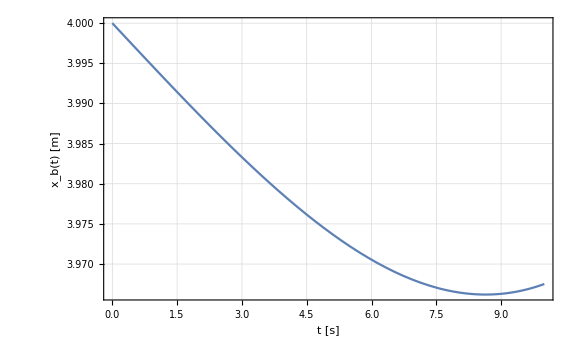
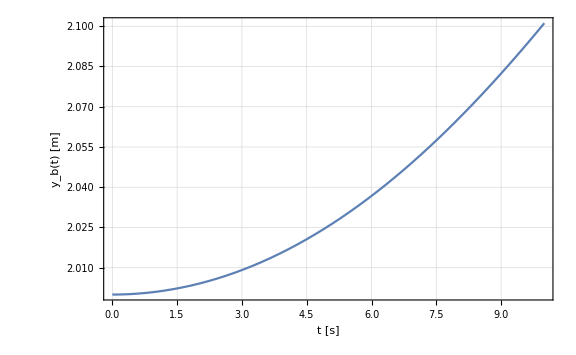
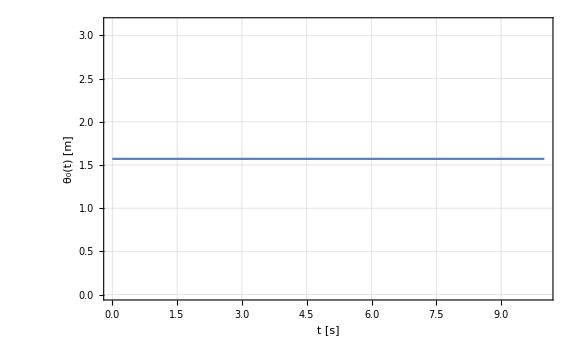
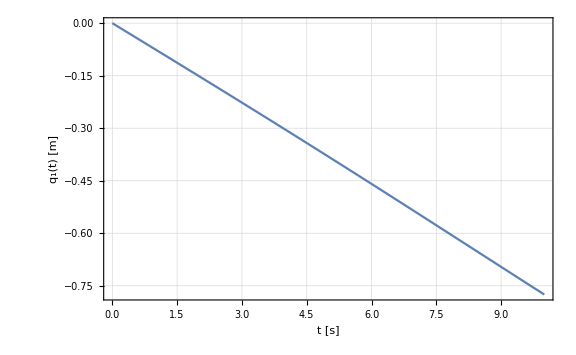
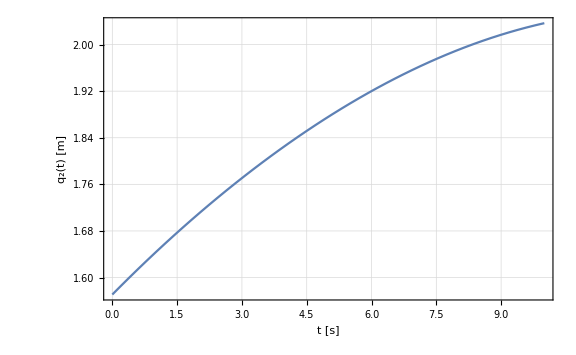

```mathematica
Row[{Plot[solMotion1[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion1[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

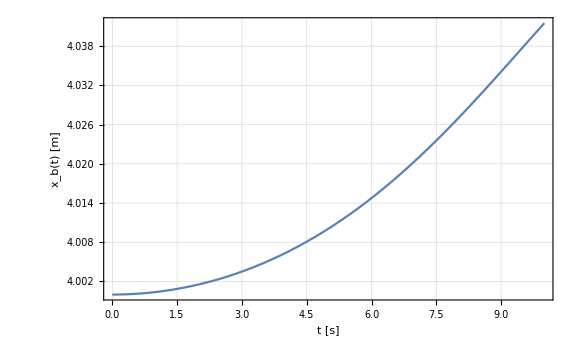
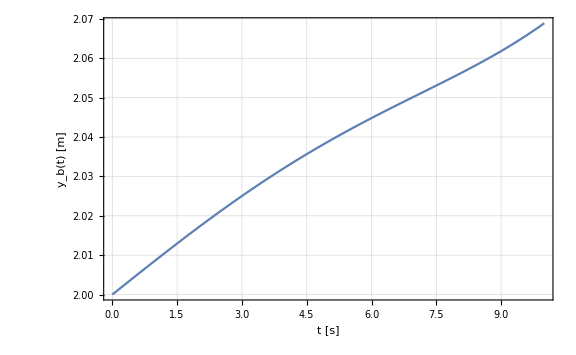
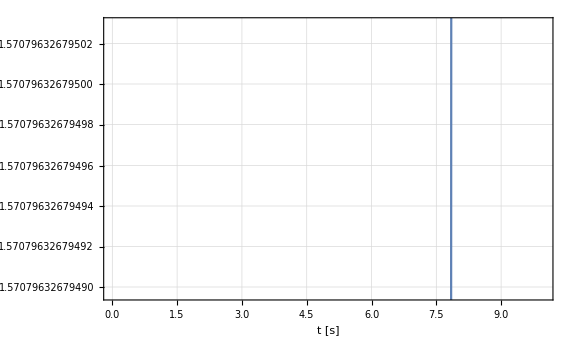
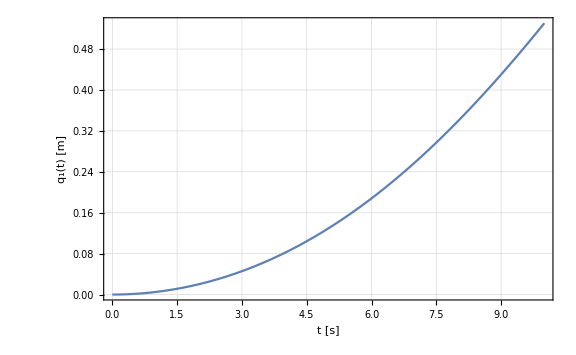
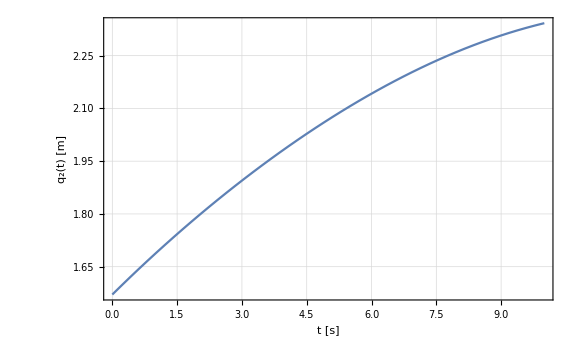

```mathematica
Row[{Plot[solMotion2[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotion2[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

```mathematica
RobotPlot=ListLinePlot[{Ob[[1;;2]]/.param/.paramScheme,O1[[1;;2]]/.param/.paramScheme,EE[[1;;2]]/.param/.paramScheme},PlotMarkers->{Automatic, 5}];
```

```mathematica
{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10}
{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10}
```

{{3.96752,2.10114},{8.94323,7.17996},{2.17049,9.34377}}

{{4.04153,2.06891},{0.443502,8.20131},{-1.44372,1.34635}}

```mathematica
RobotPlotAfter1=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion1/.t->10,O1[[1;;2]]/.param/.solMotion1/.t->10,EE[[1;;2]]/.param/.solMotion1/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
RobotPlotAfter2=ListLinePlot[{Ob[[1;;2]]/.param/.solMotion2/.t->10,O1[[1;;2]]/.param/.solMotion2/.t->10,EE[[1;;2]]/.param/.solMotion2/.t->10},PlotRange->Automatic,PlotMarkers->{Automatic, 5},PlotStyle->Dashed];
```

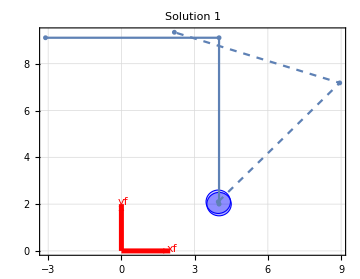
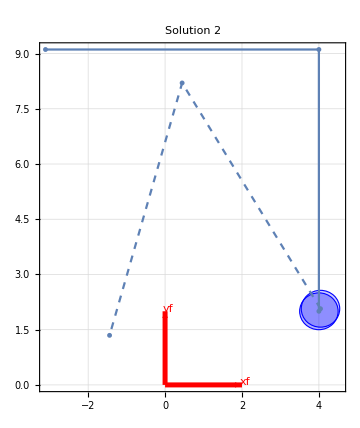

```mathematica
Row[{Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion1/.t->10,r]}]],RobotPlot,RobotPlotAfter1,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 1",ImageSize->Medium],Show[{Block[{r=0.5},Graphics[{Blue,EdgeForm[Thick],Opacity[0.3],Disk[Ob[[1;;2]]/.param/.paramScheme,r]}]],Block[{r=0.5},Graphics[{Blue,EdgeForm[{Thick,Dashed}],Opacity[0.2],Disk[Ob[[1;;2]]/.param/.solMotion2/.t->10,r]}]],RobotPlot,RobotPlotAfter2,RF0arrow[1],RF0arrow[2]},Frame->True,GridLines->Automatic,PlotRange->Automatic,PlotLabel->"Solution 2",ImageSize->Medium]}]
```

### Simulation with control

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=1IdentityMatrix[5];
Kv=2 Sqrt[Kp];
```

```mathematica
pd={xb[t],yb[t],θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0,0,0};
```

{4,2,π/2,0,π/2}

```mathematica
U=-Mp.(Kv.(p'-pd')+Kp.(p-pd))+Cp;
```

```mathematica
eqMotionControl=Mp.D[p,t,t]+Cp-U;
eqMotionControlDirect=D[p,t,t]+Kv.(p'-pd')+Kp.(p-pd)
```

{-4+xb[t]+2 xb'[t]+xb''[t],-2+yb[t]+2 yb'[t]+yb''[t],-π/2+θ0[t]+2 θ0'[t]+θ0''[t],q1[t]+2 q1'[t]+q1''[t],-π/2+q2[t]+2 q2'[t]+q2''[t]}

```mathematica
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotionControl2=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,15},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

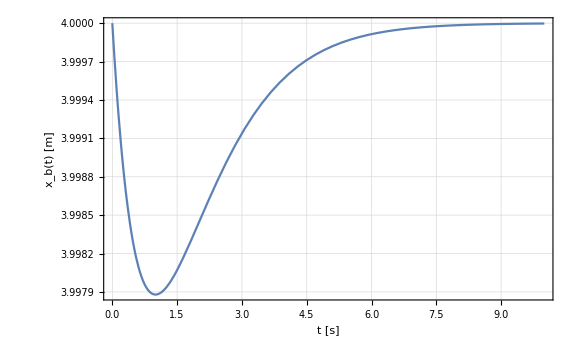
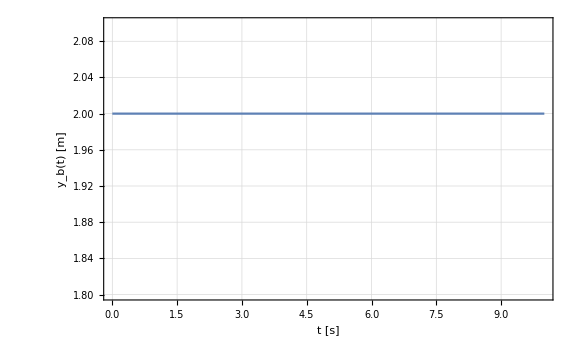
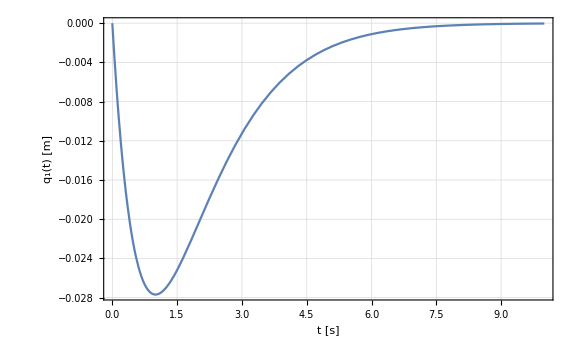
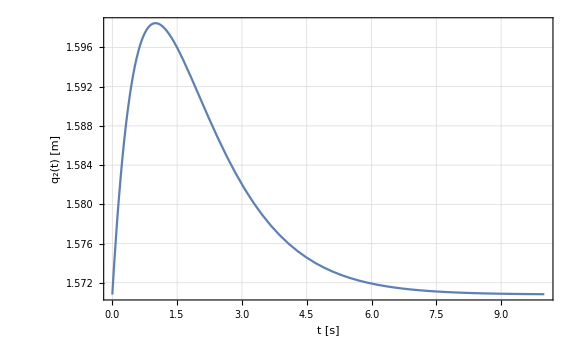
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl1[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[solMotionControl1[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl1[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

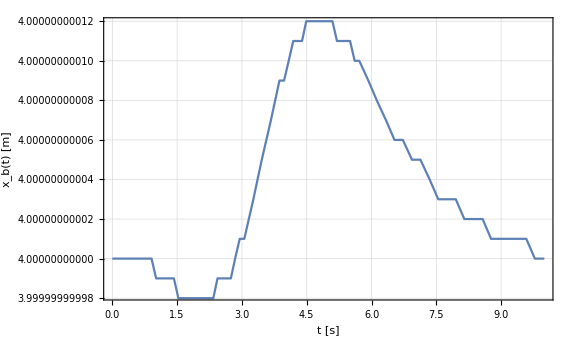
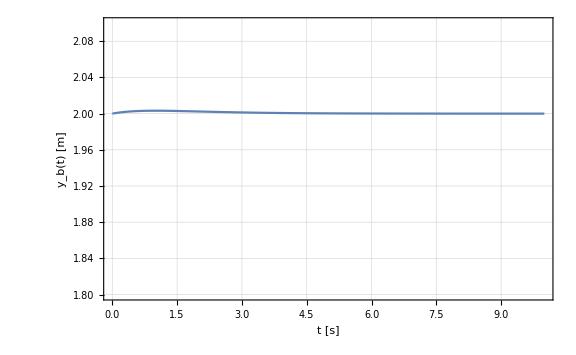
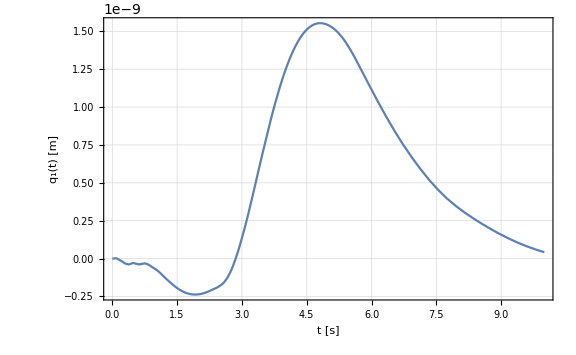
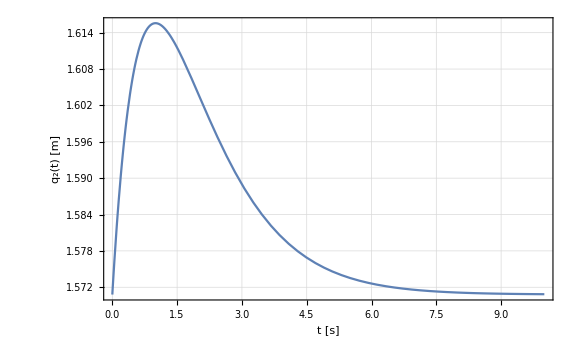
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl2[[1,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[2,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[solMotionControl2[[3,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[4,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[5,2]],{t,0,10},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

### Simulation with uknown mass

#### PID

Let’s suppose a critical damped behaviour (i.e. ξ=1):

```mathematica
Kp=1IdentityMatrix[5];
Kv=2 Sqrt[Kp];
```

```mathematica
pd={xb[t],yb[t],θ0[t],q1[t],q2[t]}/.paramScheme
pd'={0,0,0,0,0};
```

{4,2,π/2,0,π/2}

```mathematica
test=0.1;
```

```mathematica
Mpstim=Mp/.mO->test;Mpstim/.param/.paramScheme//MatrixForm
Cpstim=Cp/.mO->test;Mp/.param/.paramScheme//MatrixForm
```

(11336.1 | -3.47263×10^-18 | -7124.93 | -7124.93 | 2.46904×10^-17
-3.47263×10^-18 | 11336.1 | -2375.35 | -2375.35 | -2375.35
-7124.93 | -2375.35 | 56696.9 | 56290.7 | 11260.6
-7124.93 | -2375.35 | 56290.7 | 56290.7 | 11260.6
2.46904×10^-17 | -2375.35 | 11260.6 | 11260.6 | 11260.6)

(12336. | -3.47263×10^-14 | -14234.2 | -14234.2 | 2.46904×10^-13
-3.47263×10^-14 | 12194.2 | -8476.68 | -8476.68 | -8476.68
-14234.2 | -8476.68 | 150624. | 150218. | 54641.
-14234.2 | -8476.68 | 150218. | 150218. | 54641.
2.46904×10^-13 | -8476.68 | 54641. | 54641. | 54641.)

```mathematica
U=-Mpstim.(Kv.(p'-pd')+Kp.(p-pd))+Cpstim;
```

```mathematica
eqMotionControl=Mp.D[p,t,t]+Cp-U;
eqMotionControlDirect=Mp.D[p,t,t]+Kv.(p'-pd')+Kp.(p-pd);
```

```mathematica
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotionControl2=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

```mathematica
Clear[ξ1,m11,mOreal1,mOreal2,mOreal4,mOreal5,i,m22,ξ2,Mtest,Cptest]
```

```mathematica
For[overshoot1=1;overshootTest=2;i=1;Mtest=Mp/.mO->test;
Cptest=Cp/.mO->test;U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;eqMotionControl=Mp.D[p,t,t]+Cp-U,i<10;overshoot1>10^-10,i++;
ξ1=-Log[overshoot1]/Sqrt[π^2+Log[overshoot1]^2];
m11=((Mtest/.param/.paramScheme)[[1,1]])/Sqrt[ξ1];
Mtest=Mp/.mO->mOreal1;
Cptest=Cp/.mO->mOreal1;
U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;
eqMotionControl=Mp.D[p,t,t]+Cp-U,
overshootTest=overshoot;
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]];overshoot1=Abs[FindMaximum[solMotionControl1[[1,2]]-(xb[t]/.paramScheme),{t,5,10}][[1]]];
Print[{overshoot1,mOreal1}];
mOreal1=Solve[Mp[[1,1]]-m11==0,mO][[1,1,2]]/.param/.paramScheme]
```

{0.000201394,mOreal1}

{0.0000352708,368.005}

{0.0000352708,368.005}

{4.19576×10^-6,633.567}

{4.19576×10^-6,633.567}

{1.34324×10^-7,821.737}

{1.34324×10^-7,821.737}

{1.72371×10^-10,939.821}

{1.72371×10^-10,939.821}

{Abs[-4+InterpolatingFunction[…][t]],999.317}

```mathematica
mOreal1
```

999.317

```mathematica
For[overshoot2=1;i=1;Mtest=Mp/.mO->test;
Cptest=Cp/.mO->test;U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;eqMotionControl=Mp.D[p,t,t]+Cp-U,i<5;overshoot2>10^-13,i++;
ξ2=-Log[overshoot2]/Sqrt[π^2+Log[overshoot2]^2];
m22=((Mtest/.param/.paramScheme)[[2,2]])/Sqrt[ξ2];
mOreal2=Solve[Mp[[2,2]]-m22==0,mO][[1,1,2]]/.param/.paramScheme;
Mtest=Mp/.mO->mOreal2;
Cptest=Cp/.mO->mOreal2;
U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;
eqMotionControl=Mp.D[p,t,t]+Cp-U,
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]];overshoot2=Abs[FindMinimum[solMotionControl1[[2,2]]-(yb[t]/.paramScheme),{t,5,10}][[1]]];
Print[{overshoot2,mOreal2}]]
```

{0.0000125353,mOreal2}

{2.67303×10^-7,248.816}

{5.2077×10^-7,391.491}

{9.81915×10^-10,549.046}

{1.65513×10^-10,627.282}

{3.04956×10^-11,694.1}

{1.59606×10^-12,752.244}

{1.7677×10^-12,798.698}

{1.49547×10^-12,845.656}

{3.64153×10^-14,892.199}

```mathematica
mOreal2
```

928.395

```mathematica
For[overshoot4=1;i=1;Mtest=Mp/.mO->test;
Cptest=Cp/.mO->test;U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;eqMotionControl=Mp.D[p,t,t]+Cp-U,i<5;overshoot4>10^-11,i++;
ξ4=-Log[overshoot4]/Sqrt[π^2+Log[overshoot4]^2];
m44=((Mtest/.param/.paramScheme)[[3,3]])/Sqrt[ξ4];
mOreal4=Solve[Mp[[4,4]]-m44==0,mO][[1,1,2]]/.param/.paramScheme;
Mtest=Mp/.mO->mOreal4;
Cptest=Cp/.mO->mOreal4;
U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;
eqMotionControl=Mp.D[p,t,t]+Cp-U,
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]];overshoot4=Abs[FindMaximum[solMotionControl1[[4,2]]-(q1[t]/.paramScheme),{t,5,10}][[1]]];
Print[{overshoot4,mOreal4}]]
```

{0.00262581,mOreal4}

{0.00220693,42.7829}

{0.00184146,86.0661}

{0.00152464,129.787}

{0.00125163,173.78}

{0.00101806,217.88}

{0.000819648,261.92}

{0.00065249,305.735}

{0.000512981,349.163}

{0.000397677,392.042}

{0.000303493,434.217}

{0.000227571,475.537}

{0.000167276,515.858}

{0.000120203,555.042}

{0.0000841813,592.96}

{0.0000572514,629.493}

{0.0000376435,664.533}

{0.0000237707,697.984}

{0.0000143473,729.754}

{8.21076×10^-6,759.776}

{4.40907×10^-6,787.993}

{2.19638×10^-6,814.363}

{1.00199×10^-6,838.861}

{4.09261×10^-7,861.484}

{1.44861×10^-7,882.236}

{4.24106×10^-8,901.126}

{8.4432×10^-9,918.17}

{2.39886×10^-9,933.243}

{9.77568×10^-11,947.102}

{1.79523×10^-10,958.577}

{3.89194×10^-11,970.499}

{5.29943×10^-11,981.538}

{Abs[InterpolatingFunction[…][t]],992.802}

```mathematica
mOreal4=992.801766
```

992.802

```mathematica
For[overshoot5=1;i=1;Mtest=Mp/.mO->test;
Cptest=Cp/.mO->test;U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;eqMotionControl=Mp.D[p,t,t]+Cp-U,i<5;overshoot5>10^-10,i++;
ξ5=-Log[overshoot5]/Sqrt[π^2+Log[overshoot5]^2];
m55=((Mtest/.param/.paramScheme)[[5,5]])/Sqrt[ξ5];
mOreal5=Solve[Mp[[5,5]]-m55==0,mO][[1,1,2]]/.param/.paramScheme;
Mtest=Mp/.mO->mOreal5;
Cptest=Cp/.mO->mOreal5;
U=-Mtest.(Kv.(p'-pd')+Kp.(p-pd))+Cptest;
eqMotionControl=Mp.D[p,t,t]+Cp-U,
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]];overshoot5=Abs[FindMinimum[solMotionControl1[[5,2]]-(q2[t]/.paramScheme),{t,5,10}][[1]]];
Print[{overshoot5,mOreal5}]]
```

{0.00290822,mOreal5}

{0.00269344,17.1263}

{0.0024877,34.8426}

{0.00229093,53.2394}

{0.00210319,72.3036}

{0.00192436,92.0179}

{0.00175474,112.361}

{0.00159421,133.308}

{0.00144268,154.83}

{0.00130029,176.894}

{0.00116688,199.463}

{0.00104242,222.497}

{0.000926822,245.952}

{0.000819909,269.782}

{0.000721493,293.935}

{0.000631341,318.361}

{0.000549163,343.004}

{0.000474751,367.806}

{0.0004077,392.711}

{0.000347643,417.658}

{0.000294255,442.586}

{0.000247058,467.435}

{0.000205666,492.144}

{0.000169652,516.652}

{0.000138574,540.898}

{0.000112004,564.824}

{0.0000895103,588.372}

{0.0000706733,611.487}

{0.000055075,634.115}

{0.000042314,656.208}

{0.0000319853,677.716}

{0.0000237883,698.593}

{0.000017375,718.801}

{0.000012444,738.302}

{8.72353×10^-6,757.066}

{5.97506×10^-6,775.064}

{3.98793×10^-6,792.273}

{2.59097×10^-6,808.676}

{1.63538×10^-6,824.259}

{9.98046×10^-7,839.017}

{5.8784×10^-7,852.946}

{3.31733×10^-7,866.048}

{1.8149×10^-7,878.323}

{9.20523×10^-8,889.8}

{4.37363×10^-8,900.454}

{1.6358×10^-8,910.296}

{7.61294×10^-9,919.173}

{2.67262×10^-9,927.409}

{9.13075×10^-10,934.854}

{2.14646×10^-9,941.598}

{1.03482×10^-10,948.969}

{1.68537×10^-10,954.57}

{5.24059×10^-10,960.443}

{4.17488×10^66,966.981}

{Abs[-π/2+{}⟦1⟧⟦5,2⟧],-259.452-1226.56 ⅈ}

```mathematica
mOreal5=966.981182530030
```

966.981

```mathematica
mOreal1
mOreal2
mOreal4
mOreal5
```

999.317

928.395

992.802

966.981

```mathematica
realmass=Mean[{mOreal1,mOreal2,mOreal4,mOreal5}]
error=(1-realmass/(mO/.param))*100
```

971.874

2.81262

```mathematica
paramIteration={xb[t]->solMotionControl1[[1,2]],yb[t]->solMotionControl1[[2,2]],θ0[t]->solMotionControl1[[3,2]],q1[t]->solMotionControl1[[4,2]],q2[t]->solMotionControl1[[5,2]],xb'[t]->D[solMotionControl1[[1,2]],t],yb'[t]->D[solMotionControl1[[2,2]],t],θ0'[t]->D[solMotionControl1[[3,2]],t],q1'[t]->D[solMotionControl1[[4,2]],t],q2'[t]->D[solMotionControl1[[5,2]],t],xb''[t]->D[solMotionControl1[[1,2]],t,t],yb''[t]->D[solMotionControl1[[2,2]],t,t],θ0''[t]->D[solMotionControl1[[3,2]],t,t],q1''[t]->D[solMotionControl1[[4,2]],t,t],q2''[t]->D[solMotionControl1[[5,2]],t,t]};
```

```mathematica
Mpstim=Mp/.mO->realmass;Mpstim/.param/.paramScheme//MatrixForm
Cpstim=Cp/.mO->realmass;Mp/.param/.paramScheme//MatrixForm
```

(12307.9 | -3.37496×10^-14 | -14034.2 | -14034.2 | 2.3996×10^-13
-3.37496×10^-14 | 12170.1 | -8305.05 | -8305.05 | -8305.05
-14034.2 | -8305.05 | 147982. | 147576. | 53420.8
-14034.2 | -8305.05 | 147576. | 147576. | 53420.8
2.3996×10^-13 | -8305.05 | 53420.8 | 53420.8 | 53420.8)

(12336. | -3.47263×10^-14 | -14234.2 | -14234.2 | 2.46904×10^-13
-3.47263×10^-14 | 12194.2 | -8476.68 | -8476.68 | -8476.68
-14234.2 | -8476.68 | 150624. | 150218. | 54641.
-14234.2 | -8476.68 | 150218. | 150218. | 54641.
2.46904×10^-13 | -8476.68 | 54641. | 54641. | 54641.)

```mathematica
U=-Mpstim.(Kv.(p'-pd')+Kp.(p-pd))+Cpstim;
```

```mathematica
eqMotionControl=Mp.D[p,t,t]+Cp-U;
eqMotionControlDirect=Mp.D[p,t,t]+Kv.(p'-pd')+Kp.(p-pd);
```

```mathematica
solMotionControl1=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition1},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]]
solMotionControl2=NDSolve[{(eqMotionControl[[1]]/.param)==0,(eqMotionControl[[2]]/.param)==0,(eqMotionControl[[3]]/.param)==0,(eqMotionControl[[4]]/.param)==0,(eqMotionControl[[5]]/.param)==0,NDinitialCondition2},{xb[t],yb[t],θ0[t],q1[t],q2[t]},{t,0,30},Method->{"EquationSimplification"->"Residual"}][[1]]
```

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

{xb[t]→InterpolatingFunction[…][t],yb[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],q1[t]→InterpolatingFunction[…][t],q2[t]→InterpolatingFunction[…][t]}

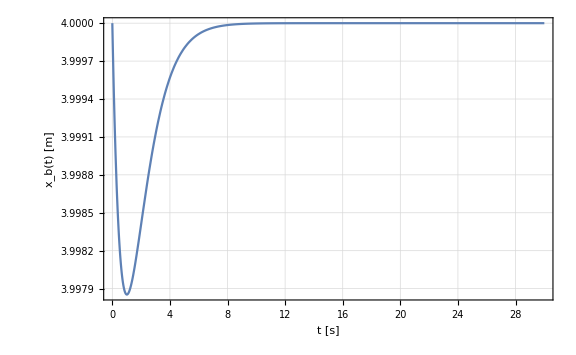
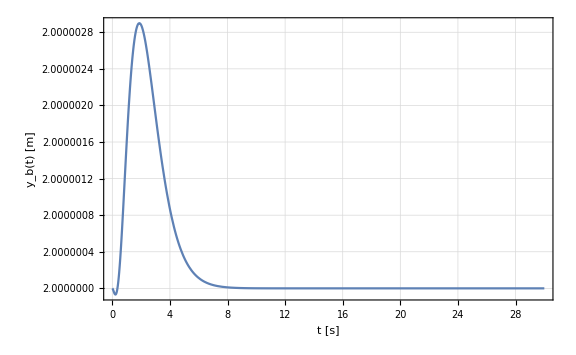
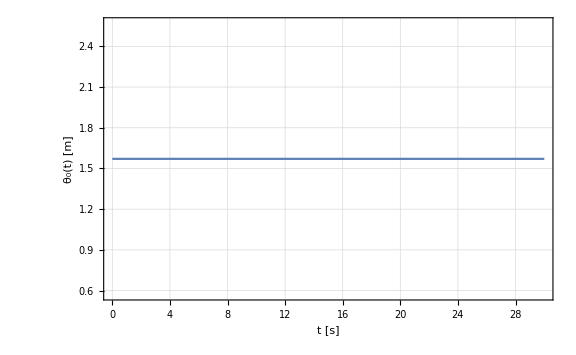
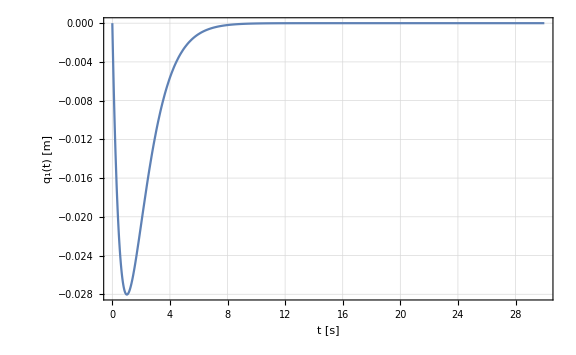
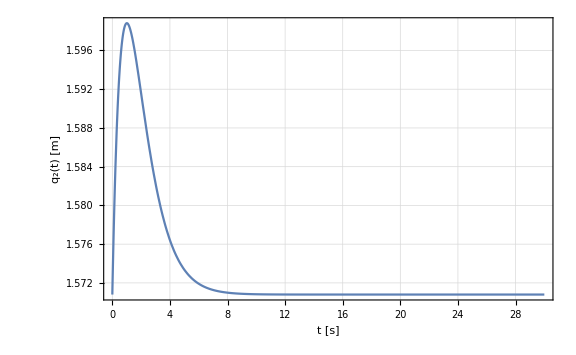

```mathematica
Row[{Plot[solMotionControl1[[1,2]],{t,0,30},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->All],
Plot[solMotionControl1[[2,2]],{t,0,30},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->All],
Plot[solMotionControl1[[3,2]],{t,0,30},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->All],
Plot[solMotionControl1[[4,2]],{t,0,30},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->All],
Plot[solMotionControl1[[5,2]],{t,0,30},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->All]}]
```

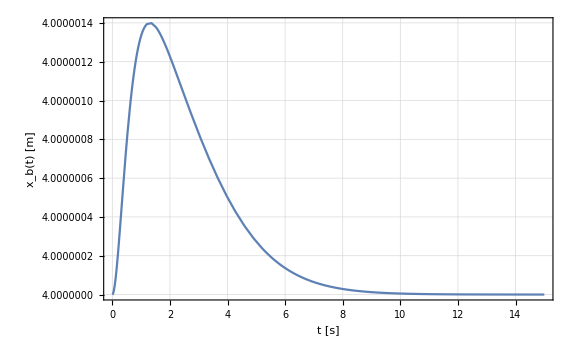
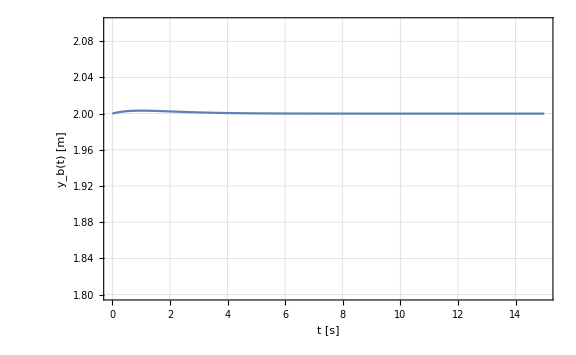
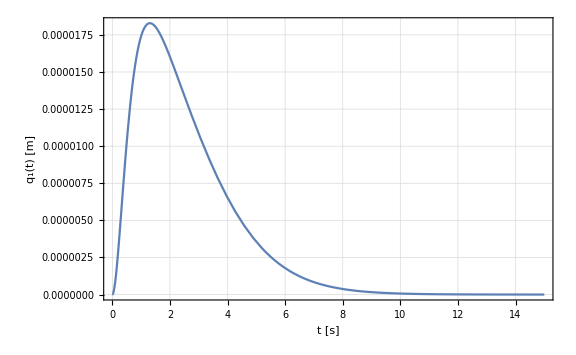
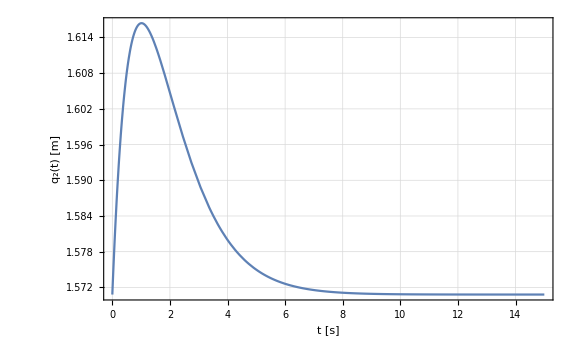
-Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[{Plot[solMotionControl2[[1,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","x_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[2,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","y_b(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618,PlotRange->{Automatic,{1.8,2.1}}],
Plot[solMotionControl2[[3,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","θ_0(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[4,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_1(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618],
Plot[solMotionControl2[[5,2]],{t,0,15},Frame->True,Axes->False,FrameLabel->{"t [s]","q_2(t) [m]"},ImageSize->Large,FrameStyle->Directive[Black],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],LabelStyle->Directive[FontFamily->"Source Serif Pro",16],Background->White,AspectRatio->1/1.618]}]
```

## Parameters Extraction

```mathematica
Mlin=Mp/.paramScheme/.paramExtraction;
```

```mathematica
Mlin//MatrixForm
```

(11336+1. mO | -3.47263×10^-17 mO | -7124.22-7.11 mO | -7124.22-7.11 mO | 2.46904×10^-16 mO
-3.47263×10^-17 mO | 11336+0.858219 mO | -2374.74-6.10194 mO | -2374.74-6.10194 mO | -2374.74-6.10194 mO
-7124.22-7.11 mO | -2374.74-6.10194 mO | 56687.5+93.9369 mO | 56281.3+93.9369 mO | 11256.3+43.3848 mO
-7124.22-7.11 mO | -2374.74-6.10194 mO | 56281.3+93.9369 mO | 56281.3+93.9369 mO | 11256.3+43.3848 mO
2.46904×10^-16 mO | -2374.74-6.10194 mO | 11256.3+43.3848 mO | 11256.3+43.3848 mO | 11256.3+43.3848 mO)

```mathematica
eqMotionControlSymbolic=Simplify[Mlin.D[p,t,t]+(Mtest/.param/.paramScheme).(Kv.(p'-pd')+Kp.(p-pd))];
```

```mathematica
initialConditionsSymbolic={xO[t]->objectPosI[[1,2]],yO[t]->objectPosI[[2,2]],Ω[t]->contactCondition,
xb'[t]->0,yb'[t]->0,θ0'[t]->0,q1'[t]->0,q2'[t]->0};
```

Initial object’s velocities without knowing Ω’[t]:

```mathematica
solVel1=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme)[[2]]]==ψf1'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme)[[3]]]==ψf1'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
solVel2=Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme)[[2]]]==ψf2'[[2]],Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme)[[3]]]==ψf2'[[3]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

xO'[t]==1.&&yO'[t]==-0.12704&&Ω'[t]==10.9768

xO'[t]==0&&yO'[t]==-1.03559&&Ω'[t]==3.07619

```mathematica
{ToRules[solVel1]}[[1]]
```

{xO'[t]→1.,yO'[t]→-0.12704,Ω'[t]→10.9768}

Initial object' s velocities knowing Ω'[t] :

```mathematica
Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf1'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf1'[[2]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
Reduce[{Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme/.Ω'[t]->0)[[1]]]==ψf2'[[1]],Chop[(ψf'/.initialConditionsSymbolic/.param/.paramScheme/.Ω'[t]->0)[[2]]]==ψf2'[[2]]},{xO'[t],yO'[t],Ω'[t]}]//Chop
```

xO'[t]==1.&&yO'[t]==0.0000115746

xO'[t]==0&&yO'[t]==-0.999988

```mathematica
momentumEq1=Chop@Simplify[M.(p'/.{p'[[1]]->pf1'[[1]],p'[[2]]->pf1'[[2]],p'[[3]]->pf1'[[3]],p'[[4]]->pf1'[[4]],p'[[5]]->pf1'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf1'[[1]],yO'[t]->ψf1'[[2]],Ω'[t]->ψf1'[[3]]})-({xO'[t],yO'[t],Ω'[t]}/.({ToRules[solVel1]}[[1]])))/.paramExtraction/.paramScheme]
Solve[momentumEq1[[1]]==0,mO][[1]]
```

{470.747-0.470747 mO,0.00219632-2.19632×10^-6 mO,-3347.02+3.34702 mO,-3347.02+3.34702 mO,-0.0156158+0.0000156158 mO}

{mO→1000.}

```mathematica
momentumEq2=Chop@Simplify[M.(p'/.{p'[[1]]->pf2'[[1]],p'[[2]]->pf2'[[2]],p'[[3]]->pf2'[[3]],p'[[4]]->pf2'[[4]],p'[[5]]->pf2'[[5]]})+Transpose[J].Transpose[pseudoInverseJop].Mo.(({xO'[t],yO'[t],Ω'[t]}/.{xO'[t]->ψf2'[[1]],yO'[t]->ψf2'[[2]],Ω'[t]->ψf2'[[3]]})-({xO'[t],yO'[t],Ω'[t]}/.({ToRules[solVel2]}[[1]])))/.paramExtraction/.paramScheme]
Solve[momentumEq2[[2]]==0,mO][[1]]
```

{0,-189.752+0.189752 mO,1349.14-1.34914 mO,1349.14-1.34914 mO,1349.14-1.34914 mO}

{mO→1000.}

From equation 4.5 (thesis):

```mathematica
transfromMatrix=Transpose[J].Transpose[pseudoInverseJop].Mo//Simplify;
```

However, this is not invertible:

```mathematica
pseudoInverseTransform=Inverse[Transpose[transfromMatrix].transfromMatrix].Transpose[transfromMatrix];
```